```mathematica
SetDirectory["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone"];
PureIntegralsNEW=ReadList[FileNameJoin[{Directory[],"files/LinearBasis-202.txt"}]];
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
$P=2^31-1;
```

```mathematica
PureIntegralsNEW[[203;;]]//Length
ReduListT=PureIntegralsNEW[[203;;]]/.hxb[n1_,n2_,n3_,n4_,n5_,n6_,n7_,n8_,n9_,n10_,n11_,n12_,n13_]:>{n1,n2,n3,n4,n5,n6,n7,n8,n9,n10,n11,n12,n13};
Sectors=ReduListT/.( n_Integer:>0/;n<0)/.( n_Integer:>1/;n>1) //DeleteDuplicates;
Sectors2=ReduListT/.( n_Integer:>0/;n<0)/.( n_Integer:>1/;n>1) ;
RemainingSectors=SortBy[Tally[Sectors2],Last]
RemainingSectors//Length
```

39

{{{0,1,1,1,0,1,1,1,1,0,0,0,0},1},{{1,0,1,1,0,1,1,1,1,0,0,0,0},1},{{1,0,1,1,1,1,1,1,0,0,0,0,0},1},{{1,1,0,1,1,1,1,1,0,0,0,0,0},1},{{1,1,1,1,1,1,1,1,1,0,0,0,0},1},{{1,1,1,1,0,1,1,1,1,0,0,0,0},3},{{1,1,1,1,1,0,1,1,1,0,0,0,0},3},{{1,1,1,1,1,1,0,1,0,0,0,0,0},3},{{1,1,1,1,1,1,0,1,1,0,0,0,0},3},{{1,1,1,1,1,1,1,1,0,0,0,0,0},3},{{1,1,1,1,0,0,1,1,1,0,0,0,0},4},{{1,1,1,1,0,1,0,1,1,0,0,0,0},4},{{1,1,1,1,1,0,1,1,0,0,0,0,0},4},{{1,1,1,1,0,1,1,1,0,0,0,0,0},7}}

14

{{123},{141}}

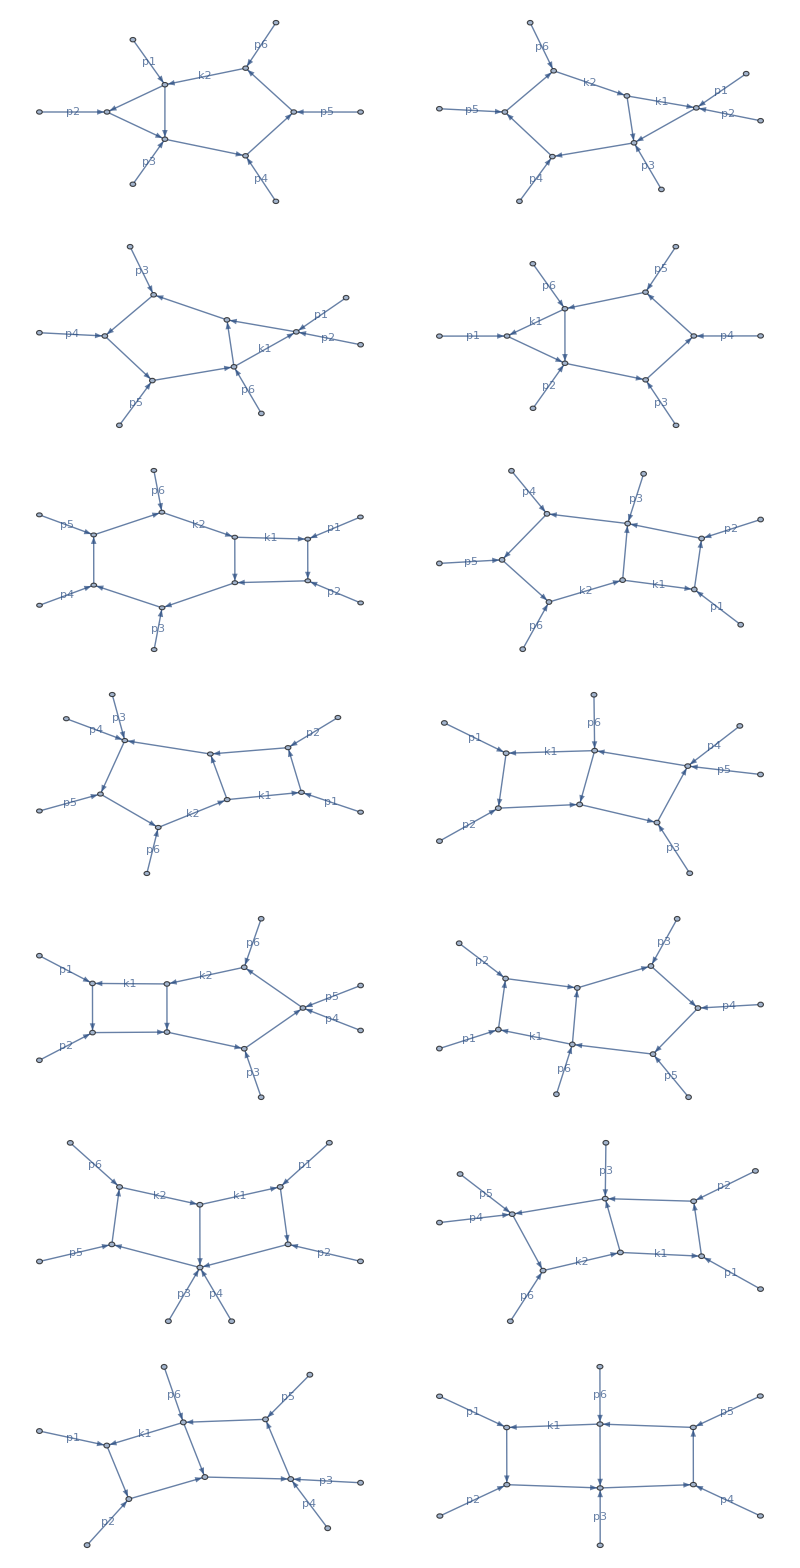

```mathematica
PlotDiagrams=Table[plotDiagram[RemainingSectors[[i,1]]],{i,1,Length[RemainingSectors]}];
Grid[ArrayReshape[PlotDiagrams,{7,2}]]
```

Cycles[{{5,14,9,12,7,11,6,10,13,8}}]

{1,2,3,4,8,11,12,13,14,6,7,9,10,5}

(1 | 1
1 | 1
3 | 4
4 | 4
7 | 3
3 | 3
3 | 1)

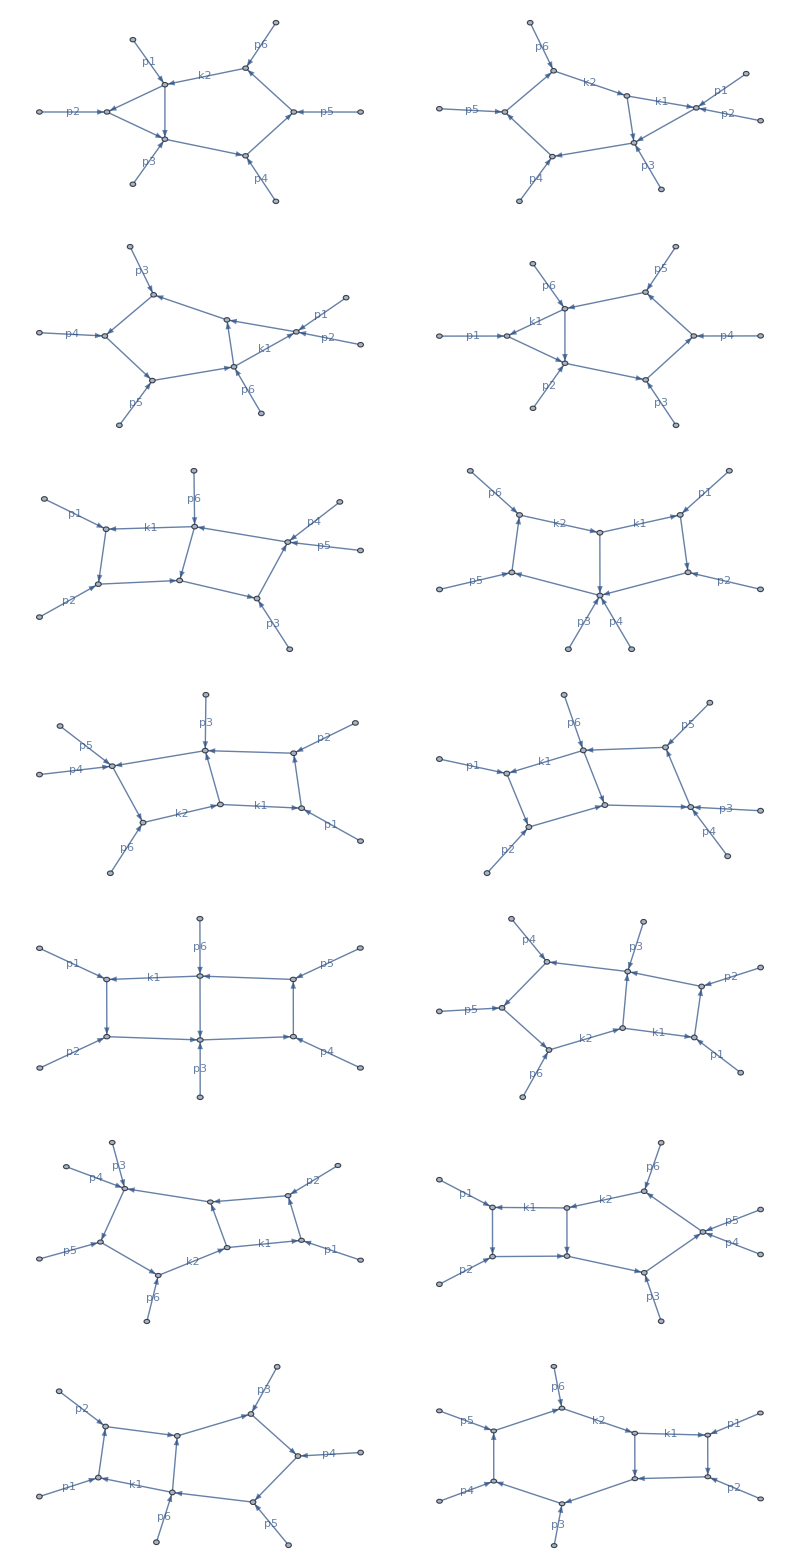

```mathematica
Form=Thread[Total[Transpose[RemainingSectors[[All,1]]]]]-1;
Permutation=FindPermutation[Form,Sort[Form]]
RemNEw=Permute[Range[1,14],Permutation]
ArrayReshape[RemainingSectors[[RemNEw]][[All,2]],{7,2}]//MatrixForm
Grid[ArrayReshape[PlotDiagrams[[RemNEw]],{7,2}]]
```

```mathematica
sectorString[sector_]:=StringForm["b``",ToString[StringJoin[Table[ToString[sector[[i]]],{i,1,Length[sector]}]]]]
Table[sectorString[RemainingSectors[[RemNEw]][[i,1]]],{i,1,13}]
```

{b1011001110000,b1011010110000,b1011101100000,b1011110100000,b0111001110000,b0111010110000,b0111011100000,b1101011100000,b1101101100000,b1101110100000,b1111001100000,b1011011100000,b1111010100000}

```mathematica
Position[Sectors2/.{n1_,n2_,n3_,n4_,n5_,n6_,n7_,n8_,n9_,n10_,n11_,n12_,n13_}:>hxb[n1,n2,n3,n4,n5,n6,n7,n8,n9,n10,n11,n12,n13],RemainingSectors[[RemNEw[[5]],1]]/.List->hxb]+202/.{n_Integer}:>n
```

{232,234,235}

```mathematica
RemNEw[[1,1]]
```